## odds ratio

```mathematica
Table[((1-CDF[NormalDistribution[5,1],x])/CDF[NormalDistribution[5,1],x])/((1-CDF[NormalDistribution[4,1],x])/CDF[NormalDistribution[4,1],x]),{x,3,6,0.2}]
```

{8.10032,7.21242,6.51802,5.98438,5.58585,5.30297,5.12184,5.03346,5.03346,5.12184,5.30297,5.58585,5.98438,6.51802,7.21242,8.10032}

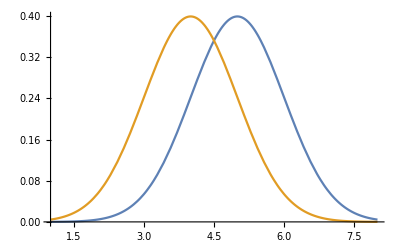

```mathematica
(* 正規分布 *)
Plot[{PDF[NormalDistribution[5,1],x],PDF[NormalDistribution[4,1],x]},{x,1,8}]
```

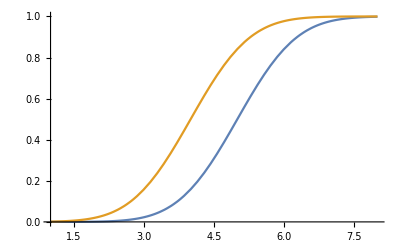

```mathematica
(* 正規分布 *)
Plot[{CDF[NormalDistribution[5,1],x],CDF[NormalDistribution[4,1],x]},{x,1,8}]
```

```mathematica
(* Odds plot *)
```

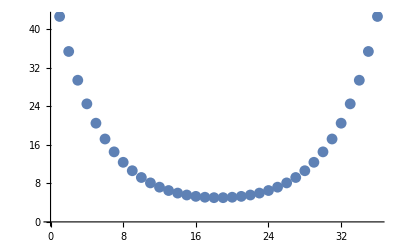

```mathematica
ListPlot[Table[((1-CDF[NormalDistribution[5,1],x])/CDF[NormalDistribution[5,1],x])/((1-CDF[NormalDistribution[4,1],x])/CDF[NormalDistribution[4,1],x]),{x,1,8,0.2}]]
```

```mathematica
(* Relative Risk plot *)
```

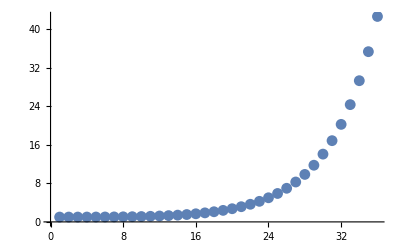

```mathematica
ListPlot[Table[(1-CDF[NormalDistribution[5,1],x])/(1-CDF[NormalDistribution[4,1],x]),{x,1,8,0.2}]]
```

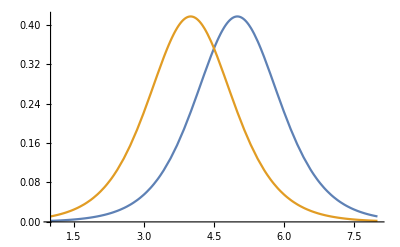

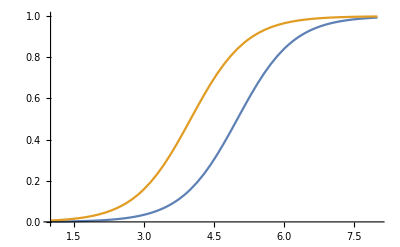

```mathematica
(* ロジスティック分布 *)
Plot[{PDF[LogisticDistribution[5,0.6],x],PDF[LogisticDistribution[4,0.6],x]},{x,1,8}]
(* ロジスティック分布 *)
Plot[{CDF[LogisticDistribution[5,0.6],x],CDF[LogisticDistribution[4,0.6],x]},{x,1,8}]
```

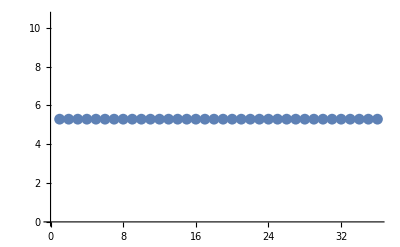

```mathematica
ListPlot[Table[((1-CDF[LogisticDistribution[5,0.6],x])/CDF[LogisticDistribution[5,0.6],x])/((1-CDF[LogisticDistribution[4,0.6],x])/CDF[LogisticDistribution[4,0.6],x]),{x,1,8,0.2}]]
```

```mathematica
(* Relative Risk plot *)
```

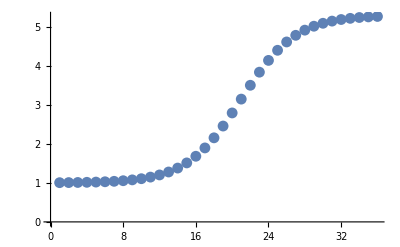

```mathematica
ListPlot[Table[(1-CDF[LogisticDistribution[5,0.6],x])/(1-CDF[LogisticDistribution[4,0.6],x]),{x,1,8,0.2}]]
```

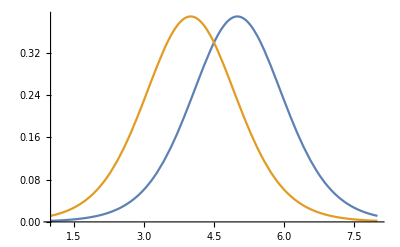

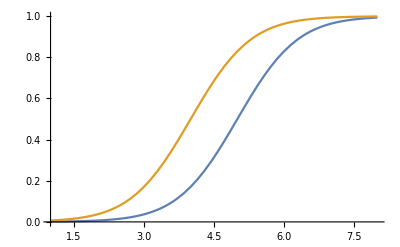

```mathematica
(* t分布 *)
Plot[{PDF[StudentTDistribution[5,1,10],x],PDF[StudentTDistribution[4,1,10],x]},{x,1,8}]
(* t分布 *)
Plot[{CDF[StudentTDistribution[5,1,10],x],CDF[StudentTDistribution[4,1,10],x]},{x,1,8}]
```

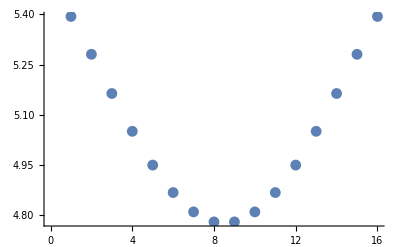

```mathematica
ListPlot[Table[((1-CDF[StudentTDistribution[5,1,10],x])/CDF[StudentTDistribution[5,1,10],x])/((1-CDF[StudentTDistribution[4,1,10],x])/CDF[StudentTDistribution[4,1,10],x]),{x,3,6,0.2}]]
```

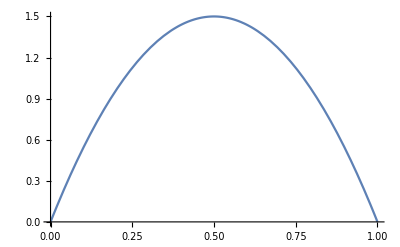

-Graphics-

```mathematica
(* beta分布 *)
Plot[{PDF[BetaDistribution[2,2],x],PDF[StudentTDistribution[3,3],x]},{x,0,1}]
(* beta布 *)
Plot[{CDF[StudentTDistribution[5,1,10],x],CDF[StudentTDistribution[4,1,10],x]},{x,1,8}]
```

```mathematica
CDF[LogisticDistribution[5,2],x]
```

1/(1+ⅇ^((5-x)/2))

```mathematica
odds[a_,b_,c_,x_]:=((a x+c)/(1-a x-c))/((a x+b)/(1-a x-b));
```

```mathematica
Plot[odds[0.1,0.1,0.3,x],{x,0,6},PlotRange->{0,4},PlotStyle->{Thick,Darker[Red]}]
```

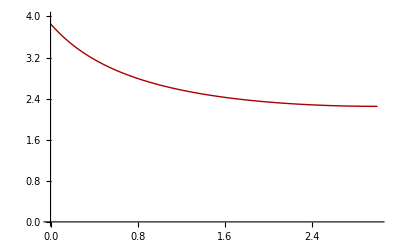

```mathematica
Plot[odds[0.1,0.1,0.3,x],{x,0,3},PlotRange->{0,4},PlotStyle->{Thick,Darker[Red]}]
```

```mathematica
D[((a x+c)/(1-a x-c))/((a x+b)/(1-a x-b)),x]//Simplify
```

```mathematica
-(a (b-c) (-1+b+c+2 a x))/((b+a x)^2 (-1+c+a x)^2)
```

-(a (b-c) (-1+b+c+2 a x))/((b+a x)^2 (-1+c+a x)^2)

```mathematica
Solve[-(a (b-c) (-1+b+c+2 a x))==0,x]
```

{{x→(1-b-c)/(2 a)}}

```mathematica
(1-b-c)/(2 a)/.{a->0.1,b->0.1,c->0.3}
```

3.

```mathematica
odds2[a_,x_]:=((a x)/(1-a x))/(x/(1-x));
```

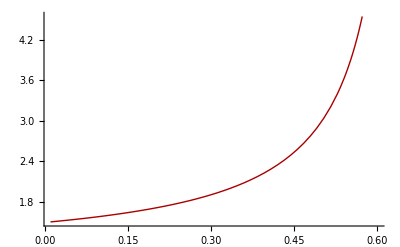

```mathematica
Plot[odds2[1.5,x],{x,0.01,0.6},PlotStyle->{Thick,Darker[Red]}]
```